```mathematica
"Project Thesis Superconductors"
"Band Gap Overlay Calculation"
"Author: Christoph Bernkopf"
```

Project Thesis Superconductors

Band Gap Overlay Calculation

Author: Christoph Bernkopf

```mathematica
(* Band Gap Overlay *)
(* Optimize these 2 Parameters with least squares fit using the experimental data expHCap & Ces Heat Capacity function *)(* For documented version of this code check out: analytical_fits.nb *)
(* Running time min. 40 secs. *)
(* Error messages for Plots surpressed using Quiet[] *)
(* Plot until end of experimental data (0.879) *)
```

```mathematica
(* Imports *)

(* Clear all variables as follows: *)
(* ClearAll["Global`*"] *)

(* Load Numerical Calculus Package *)
<<NumericalCalculus`

(* Constants *)
	kB=1.3806482*10^(-23); (* Boltzmann Constant *)
	Tc=2.05;
	AlphaBCS=1.764;
	gamma=1*kB;

(* Experimental Data *)
	jGap=Import["Documents/coding/sl_code/data/johnson_band_gap_data.csv","CSV"];
	mGap  = Import["Documents/coding/sl_code/data/muehlschlegel_data_Bandgap.csv","CSV"];
	mEnt= Import["Documents/coding/sl_code/data/muehlschlegel_data_Entropy.csv","CSV"];
	mHCap= Import["Documents/coding/sl_code/data/muehlschlegel_data_Heat_Capacity.csv","CSV"];
	expHCap= Import["Documents/coding/sl_code/data/experimental_data_Heat _Capacity.csv","CSV"];

(* Band Gap Fit *)
deltaFit = NonlinearModelFit[mGap,(1+a*T+c*T^2+e*T^3+g*T^4+i*T^5+k*T^6)/(1+b*T+d*T^2+f*T^3+h*T^4+j*T^5+l*T^6),{a,b,c,d,e,f,g,h,i,j,k,l},T];
deltaFit["ParameterTable"];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

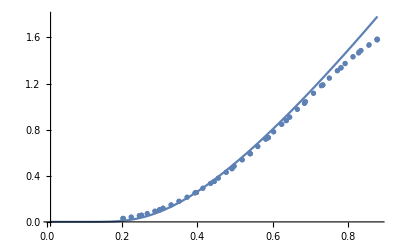

```mathematica
p1=0.85;
alpha1=1.7;
delta1[T_]:=p1*deltaFit[T]+(1-p1)*deltaFit[T]/alpha1;fx1[T_,x_]:=(Exp[AlphaBCS/T*(x^2+delta1[T]^2)^(1/2)]+1)^(-1);
Ses1[T_]:=-6*AlphaBCS/Pi^2*NIntegrate[fx1[T,x]*Log[fx1[T,x]]+(1-fx1[T,x])*Log[1-fx1[T,x]],{x,0,100}];Ces1[T_]:=T*Ses1'[T];
Quiet[Show[Plot[Ces1[T],{T,0.01,0.879}],ListPlot[expHCap]]]
```

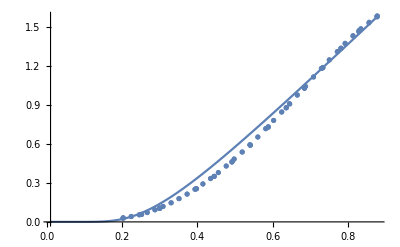

```mathematica
p2=0.6;
alpha2=2;
delta2[T_]:=p2*deltaFit[T]+(1-p2)*deltaFit[T]/alpha2;fx2[T_,x_]:=(Exp[AlphaBCS/T*(x^2+delta2[T]^2)^(1/2)]+1)^(-1);
Ses2[T_]:=-6*AlphaBCS/Pi^2*NIntegrate[fx2[T,x]*Log[fx2[T,x]]+(1-fx2[T,x])*Log[1-fx2[T,x]],{x,0,100}];Ces2[T_]:=T*Ses2'[T];
Quiet[Show[Plot[Ces2[T],{T,0.01,0.879}],ListPlot[expHCap]]]
```

```mathematica
(* Plots for Testing *)
(*
Show[ListPlot[mGap, PlotStyle->Blue], Plot[delta1[T],{T,0,1}],Frame->True]
Show[ListPlot[mGap, PlotStyle->Blue], Plot[delta2[T],{T,0,1}],Frame->True]
Plot[fx1[T,1],{T,0.01,0.879}]
Plot[fx2[T,1],{T,0.01,0.879}]
Show[Plot[Ses1[T],{T,0.01,0.879}],ListPlot[mEnt]]
Show[Plot[Ses2[T],{T,0.01,0.879}],ListPlot[mEnt]]
Show[Plot[Ces1[T],{T,0.01,0.879}],ListPlot[expHCap]]
Show[Plot[Ces2[T],{T,0.01,0.879}],ListPlot[expHCap]]
*)
```